## Collagen Numerical Eigensystems Analysis

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["./results/Parameters","Grid"]
```

/Users/htailor/Desktop/collagen_code/collagen

| 
L: | 5.
m: | 20
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Results of calculated Eigenvectors using GSL C++

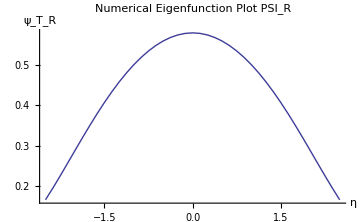
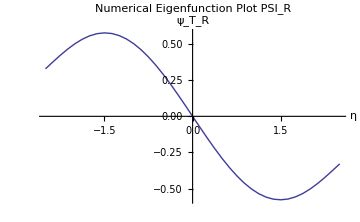
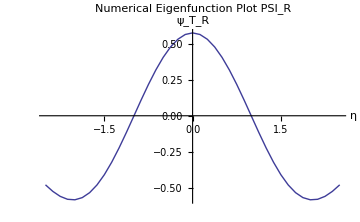
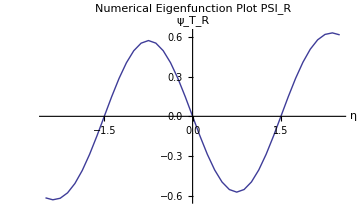

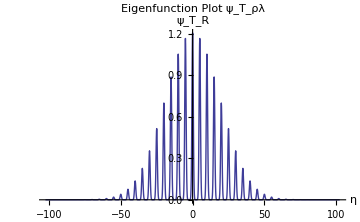
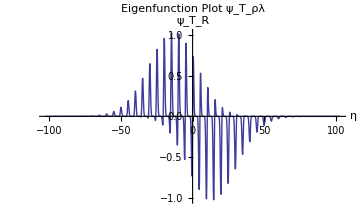
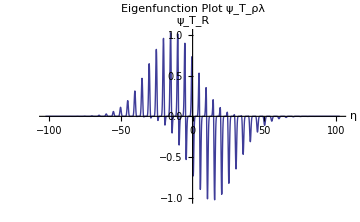
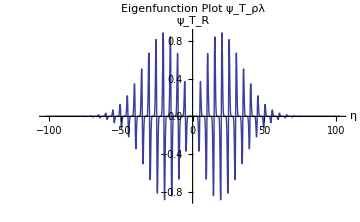

```mathematica
TR0=Import["./logs/TR/Phi_r_0.TR","Table"];
TR1=Import["./logs/TR/Phi_r_1.TR","Table"];
TR2=Import["./logs/TR/Phi_r_2.TR","Table"];
TR3=Import["./logs/TR/Phi_r_3.TR","Table"];
TR4=Import["./logs/TR/Phi_r_4.TR","Table"];
TR5=Import["./logs/TR/Phi_r_5.TR","Table"];

{ListLinePlot[{TR0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR3},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium]}

Tρλ0=Import["./logs/TROE_LAMBDA/Phi_roe_lambda0.TROE_LAMBDA","Table"];
Tρλ1=Import["./logs/TROE_LAMBDA/Phi_roe_lambda1.TROE_LAMBDA","Table"];
Tρλ2=Import["./logs/TROE_LAMBDA/Phi_roe_lambda2.TROE_LAMBDA","Table"];
Tρλ3=Import["./logs/TROE_LAMBDA/Phi_roe_lambda3.TROE_LAMBDA","Table"];
Tρλ4=Import["./logs/TROE_LAMBDA/Phi_roe_lambda4.TROE_LAMBDA","Table"];
Tρλ5=Import["./logs/TROE_LAMBDA/Phi_roe_lambda5.TROE_LAMBDA","Table"];

{ListLinePlot[{Tρλ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium],
ListLinePlot[{Tρλ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium],
ListLinePlot[{Tρλ2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium],
ListLinePlot[{Tρλ3},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρλ",ImageSize->Medium]}

TR0A=Import["./logs/R_Analytical/PSI_R_0.RA","Table"];
TR1A=Import["./logs/R_Analytical/PSI_R_1.RA","Table"];
TR2A=Import["./logs/R_Analytical/PSI_R_2.RA","Table"];
TR3A=Import["./logs/R_Analytical/PSI_R_3.RA","Table"];
TR4A=Import["./logs/R_Analytical/PSI_R_4.RA","Table"];
TR5A=Import["./logs/R_Analytical/PSI_R_5.RA","Table"];

{ListLinePlot[{TR0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR2A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR3A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium]}
```

Numerical Calculation of Eigenfunctions (Mathematica)

Functions & Eigensystem Calculation

Normalisation test for Mathematica Numerical Eigenfunctions ψ_R,ψ_ρλ

ψ_R)Discrete Normalisation ∑_(i = -m)^m ψ_R[1,i+(m+1)]ψ_R[1,i+(m+1)]Δ:

1.

ψ_ρλ)Discrete Normalisation ∑_(i = -M)^M ψ_ρλ[1,i+(M+1)]ψ_ρλ[1,i+(M+1)]Δ^2:

1.

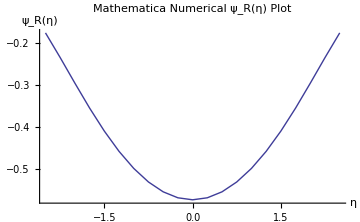
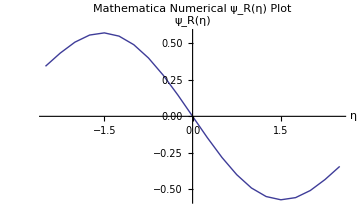
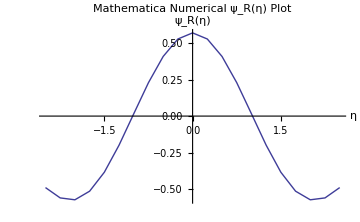

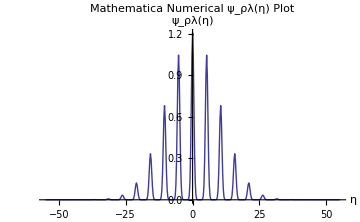
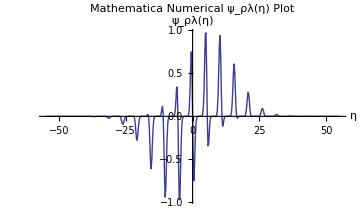
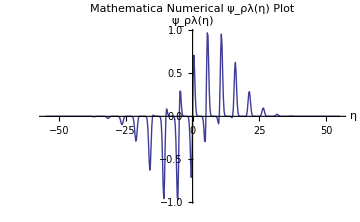
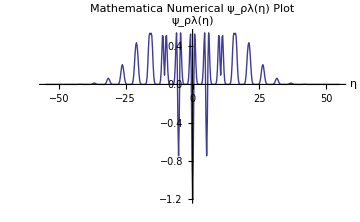

```mathematica
L=5;
m=20;
Δ=L/(2 m);
σ=1;
κ=1;
max=2 m+1;
MAX =(2 m+1)^2;
M=(MAX-1)/2;


r[x_,y_]:=(x-1)max+y;
v[x_] := 1/2 σ x^2;
V[ρ_,λ_]:=v[(2ρ)/(√κ)]+v[(ρ+√3 λ)/(√κ)]+v[(√3 λ-ρ)/(√κ)];
T[R1_, R2_] := Exp[-(R1 - R2)^2];
T̂[ ρ1_, ρ2_,λ1_,λ2_] :=   Exp[-(ρ1 - ρ2)^2]Exp[-(λ1 - λ2)^2]Exp[-V[ρ1,λ1]/2]Exp[-V[ρ2,λ2]/2];

MT = Table[Δ T[ Δ R1, Δ R2],{R1, -m, m}, {R2, -m, m}] // N;
Subscript[MT, ρ1,λ1,ρ2,λ2] = Table[  Δ^2 T̂[Δ ρ1, Δ λ1,Δ ρ2, Δ λ2], {ρ1,-m, m},{λ1,-m, m}, {ρ2, -m, m}, {λ2, -m, m}] // N;
MatrixForm[Subscript[MT, ρ1,λ1,ρ2,λ2]];
Mρλ=Table[0,{i,1,MAX},{j,1,MAX}];
Do[
Mρλ[[r[k,i],r[j,l]]]=Subscript[MT, ρ1,λ1,ρ2,λ2][[k,j]][[i,l]],
{k,1, max},
{i,1, max},
{j,1, max},
{l,1, max}
]
MatrixForm[Mρλ];

Subscript[λ, R] = Eigenvalues[MT];
Subscript[λ, ρλ] = Eigenvalues[Mρλ];

Subscript[ψ, R] = Δ^(-1/2)Eigenvectors[MT];
Subscript[ψ, ρλ] = Δ^-1 Eigenvectors[Mρλ];

Print["Normalisation test for Mathematica Numerical Eigenfunctions ψ_R,ψ_ρλ"]
Print["ψ_R)Discrete Normalisation ∑_(i = -m)^m ψ_R[1,i+(m+1)]ψ_R[1,i+(m+1)]Δ:"]
∑_(i=-m)^m Subscript[ψ, R][[1,i+(m+1)]]Subscript[ψ, R][[1,i+(m+1)]]Δ
Print["ψ_ρλ)Discrete Normalisation ∑_(i = -M)^M ψ_ρλ[1,i+(M+1)]ψ_ρλ[1,i+(M+1)]Δ^2:"]
∑_(i=-M)^M Subscript[ψ, ρλ][[1,i+(M+1)]]Subscript[ψ, ρλ][[1,i+(M+1)]] Δ^2

data0r = Table[{Δ (i - (m + 1)),Subscript[ψ, R][[1, i]]}, {i,1, max}] // N;
data1r = Table[{Δ (i - (m + 1)),Subscript[ψ, R][[2, i]]}, {i,1, max}] // N;
data2r = Table[{Δ (i - (m + 1)),Subscript[ψ, R][[3, i]]}, {i,1, max}] // N;


data0ρλ = Table[{Δ (i - (M + 1)),Subscript[ψ, ρλ][[1, i]]}, {i,1, MAX}] // N;
data1ρλ = Table[{Δ (i - (M + 1)),Subscript[ψ, ρλ][[2, i]]}, {i,1, MAX}] // N;
data2ρλ = Table[{Δ (i - (M + 1)),Subscript[ψ, ρλ][[3, i]]}, {i,1, MAX}] // N;
data3ρλ = Table[{Δ (i - (M + 1)),Subscript[ψ, ρλ][[4, i]]}, {i,1, MAX}] // N;

{ListLinePlot[data0r,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_R(η)  Plot", AxesLabel -> {η, "ψ_R(η)"}],
ListLinePlot[data1r,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_R(η)  Plot", AxesLabel -> {η, "ψ_R(η)"}],
ListLinePlot[data2r,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_R(η)  Plot",AxesLabel -> {η, "ψ_R(η)"}]}


{ListLinePlot[data0ρλ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρλ(η)  Plot", AxesLabel -> {η, "ψ_ρλ(η)"}],
ListLinePlot[data1ρλ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρλ(η)  Plot", AxesLabel -> {η, "ψ_ρλ(η)"}],
ListLinePlot[data2ρλ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_ρλ(η)  Plot",AxesLabel -> {η, "ψ_ρλ(η)"}],
ListLinePlot[data3ρλ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_ρλ(η)  Plot",AxesLabel -> {η, "ψ_ρλ(η)"}]}
```

Comparasion of ψ_(ρ,λ) Eigenfunctions

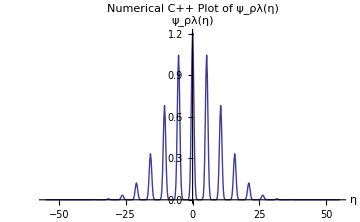
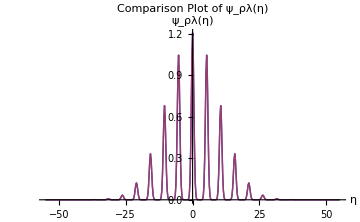
{-Graphics-,-Graphics-,-Graphics-}

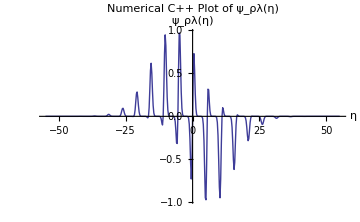
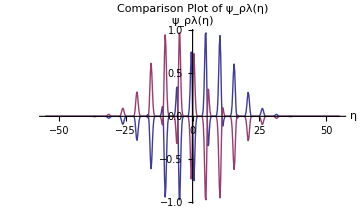
{-Graphics-,-Graphics-,-Graphics-}

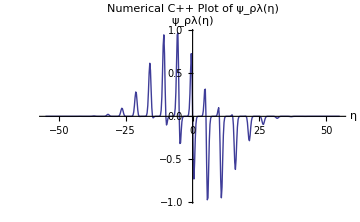
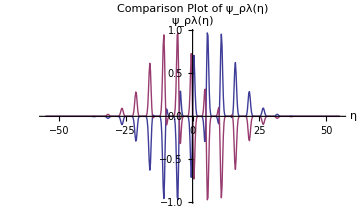
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[data0ρλ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρλ(η)  Plot", AxesLabel -> {η, "ψ_ρλ(η)"}],
ListLinePlot[{Tρλ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρλ(η)"},PlotLabel->"Numerical C++ Plot of ψ_ρλ(η)",ImageSize->Medium],
ListLinePlot[{data0ρλ,Tρλ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρλ(η)"},PlotLabel->"Comparison Plot of ψ_ρλ(η)",ImageSize->Medium]}

{ListLinePlot[data1ρλ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρλ(η)  Plot", AxesLabel -> {η, "ψ_ρλ(η)"}],
ListLinePlot[{Tρλ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρλ(η)"},PlotLabel->"Numerical C++ Plot of ψ_ρλ(η)",ImageSize->Medium],
ListLinePlot[{data1ρλ,Tρλ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρλ(η)"},PlotLabel->"Comparison Plot of ψ_ρλ(η)",ImageSize->Medium]}

{ListLinePlot[data2ρλ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρλ(η)  Plot", AxesLabel -> {η, "ψ_ρλ(η)"}],
ListLinePlot[{Tρλ2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρλ(η)"},PlotLabel->"Numerical C++ Plot of ψ_ρλ(η)",ImageSize->Medium],
ListLinePlot[{data2ρλ,Tρλ2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρλ(η)"},PlotLabel->"Comparison Plot of ψ_ρλ(η)",ImageSize->Medium]}
```